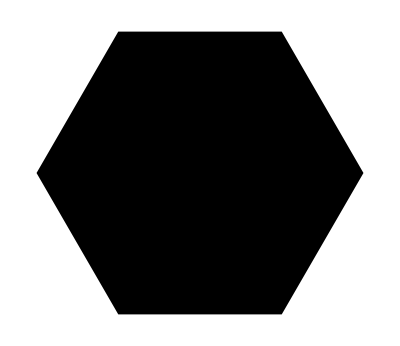
TriangulateMesh[-Graphics-]

```mathematica
TriangulateMesh[Region[RegularPolygon[6]]]
```

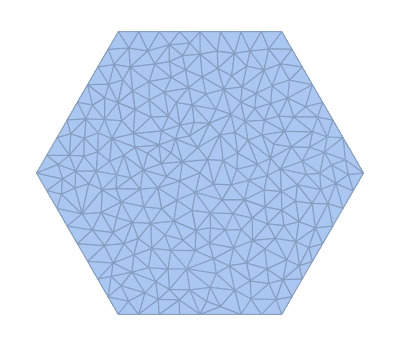

```mathematica
DiscretizeRegion[Region[RegularPolygon[6]]]
```

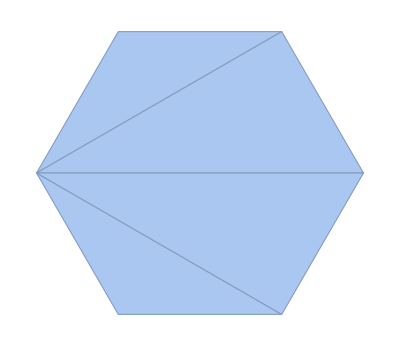

```mathematica
DiscretizeRegion[Region[RegularPolygon[6]],MaxCellMeasure->∞]
```

```mathematica
CatalanNumber[4]
```

14

```mathematica
CatalanNumber[3]
```

5

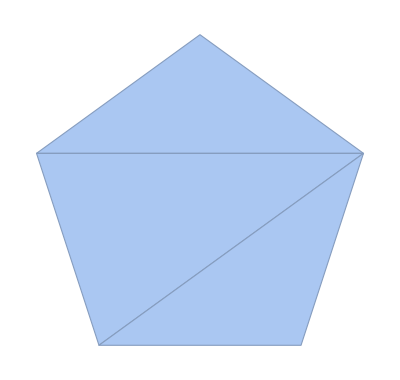

```mathematica
DiscretizeRegion[RegularPolygon[5],MaxCellMeasure->∞]
```

```mathematica
CatalanNumber[4-2]
```

2

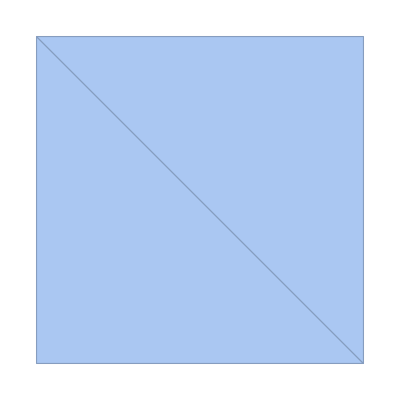

```mathematica
DiscretizeRegion[RegularPolygon[4],MaxCellMeasure->∞]
```

```mathematica
CatalanNumber[1]
```

1

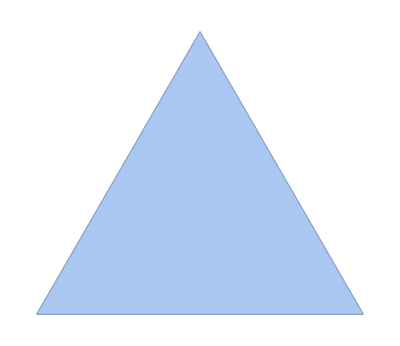

```mathematica
DiscretizeRegion[RegularPolygon[3],MaxCellMeasure->∞]
```

```mathematica
?RegularPolygonTriangulations
```

```mathematica
RegularPolygonTriangulations[4]
```

{}

```mathematica
Quit
```

```mathematica
triangulations = Table[Last/@Select[Sort[Map[{linechecker[#],#}&,Sort/@Subsets[Sort[Drop[Flatten[Reverse[Table[{a,b},{a,1,sides-2},{b,a+2,sides}]],1],-1]],{sides-3}]]],First[#]==True&],{sides,5,8}];
```

```mathematica
Remove[triangulations]
```

```mathematica
crosscheck//ClearAll
crosscheck[{{aa_,bb_},{cc_,dd_}}] :=
 If[Length[Union[{aa,bb,cc,dd}]]==3, True,
If[bb<cc || bb>dd,True,False]]
linechecker//ClearAll
linechecker[zz_List] := If[Union[Map[crosscheck[#]&,Subsets[zz,{2}]]]=={True},True,False]
triangulations//ClearAll
triangulations[k_]:= Table[Last/@Select[Sort[Map[{linechecker[#],#}&,Sort/@Subsets[Sort[Drop[Flatten[Reverse[Table[{a,b},{a,1,sides-2},{b,a+2,sides}]],1],-1]],{sides-3}]]],First[#]==True&],{sides,{k}}];
```

```mathematica
triangulations[5]
```

{{{{1,3},{1,4}},{{1,3},{3,5}},{{1,4},{2,4}},{{2,4},{2,5}},{{2,5},{3,5}}}}

```mathematica
pts=Table[N[{Cos[x],Sin[x]}],{x,(2π)/5,2π,2 π/5}]
```

{{0.309017,0.951057},{-0.809017,0.587785},{-0.809017,-0.587785},{0.309017,-0.951057},{1.,0.}}

```mathematica
pts
```

{{0.309017,0.951057},{-0.809017,0.587785},{-0.809017,-0.587785},{0.309017,-0.951057},{1.,0.}}

```mathematica
First[triangulations[5]]
```

{{{1,3},{1,4}},{{1,3},{3,5}},{{1,4},{2,4}},{{2,4},{2,5}},{{2,5},{3,5}}}

```mathematica
RegularPolygonTriangulations[6]
```

{{0.5,0.866025},{-0.5,0.866025},{-1.,0.},{-0.5,-0.866025},{0.5,-0.866025},{1.,0.}}

```mathematica
RegularPolygonTriangulations[7]
```

{{0.62349,0.781831},{-0.222521,0.974928},{-0.900969,0.433884},{-0.900969,-0.433884},{-0.222521,-0.974928},{0.62349,-0.781831},{1.,0.}}

```mathematica
Map[pts]
```

```mathematica
triangulations=.
```

```mathematica
triangulations[k_]:= Table[Last/@Select[Sort[Map[{linechecker[#],#}&,Sort/@Subsets[Sort[Drop[Flatten[Reverse[Table[{a,b},{a,1,sides-2},{b,a+2,sides}]],1],-1]],{sides-3}]]],First[#]==True&],{sides,{k}}];
```

```mathematica
triangulations[5]
```

{{{{1,3},{1,4}},{{1,3},{3,5}},{{1,4},{2,4}},{{2,4},{2,5}},{{2,5},{3,5}}}}

```mathematica
triangulations[6]
```

{{{{1,3},{1,4},{1,5}},{{1,3},{1,4},{4,6}},{{1,3},{1,5},{3,5}},{{1,3},{3,5},{3,6}},{{1,3},{3,6},{4,6}},{{1,4},{1,5},{2,4}},{{1,4},{2,4},{4,6}},{{1,5},{2,4},{2,5}},{{1,5},{2,5},{3,5}},{{2,4},{2,5},{2,6}},{{2,4},{2,6},{4,6}},{{2,5},{2,6},{3,5}},{{2,6},{3,5},{3,6}},{{2,6},{3,6},{4,6}}}}

```mathematica
RegularPolygonTriangulations//ClearAll
RegularPolygonTriangulations[k123_]:=Block[{triangulations,sides},sides=k123;triangulations=Select[Sort[Map[{linechecker[#],#}&,Sort/@Subsets[Sort[Drop[Flatten[Reverse[Table[{a,b},{a,1,sides-2},{b,a+2,sides}]],1],-1]],{sides-3}]]],First[#]==True&](*Flatten[Table[With[{pts=Table[N[{Cos[x],Sin[x]}],{x,(2 π)/gg,2 π,(2 π)/gg}],lines=triangulations},Table[Graphics[{Line/@(pts⟦#1⟧&)/@lines⟦n⟧,Line[Append[pts,pts⟦1⟧]]},ImageSize->Small],{n,1,Length[lines]}]],{gg,{k}}]]*)]
```

```mathematica
crosscheck[{{aa_,bb_},{cc_,dd_}}] :=
 If[Length[Union[{aa,bb,cc,dd}]]==3, True,
If[bb<cc || bb>dd,True,False]]
```

```mathematica
linechecker[zz_List] := If[Union[Map[crosscheck[#]&,Subsets[zz,{2}]]]=={True},True,False]
```

```mathematica
triangulations = Table[Last/@Select[Sort[Map[{linechecker[#],#}&,Sort/@Subsets[Sort[Drop[Flatten[Reverse[Table[{a,b},{a,1,sides-2},{b,a+2,sides}]],1],-1]],{sides-3}]]],First[#]==True&],{sides,5,8}];
```

```mathematica
polygons = Table[
With[{
pts=Table[N[{Cos[x],Sin[x]}],{x,2 Pi/gg,2 Pi,2Pi/gg}],lines=triangulations[[gg-4]]},
Table[
Graphics[{
Line/@Map[pts[[#]]&,lines[[n]]],
Line[Append[pts,pts[[1]]]]},ImageSize-> {380,380}],
{n,1,Length[lines]}]],{gg,5,8}];
```

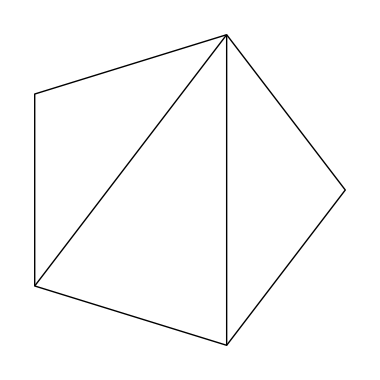

```mathematica
Take[Flatten@polygons,1]
```

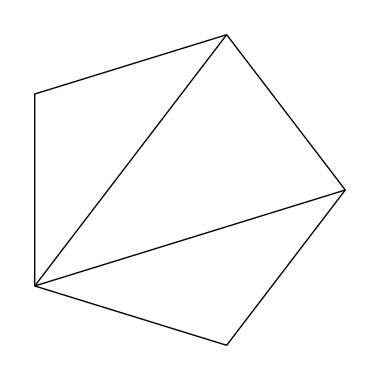
{-Graphics-,-Graphics-}

```mathematica
Take[Flatten@polygons,2]
```

```mathematica
UpValues[polygons]
```

{}

```mathematica
DownValues[polygons]
```

{}

```mathematica
Length[polygons[[1]]]
```

5

```mathematica
Length/@polygons
```

{5,14,42,132}

```mathematica
CatalanNumber[Range[3,8]]
```

{5,14,42,132,429,1430}

```mathematica
RegularPolygonTriangulations[k_]:= Flatten@Table[
With[{
pts=Table[N[{Cos[x],Sin[x]}],{x,2 Pi/gg,2 Pi,2Pi/gg}],lines=triangulations[[gg-4]]},
Table[
Graphics[{
Line/@Map[pts[[#]]&,lines[[n]]],
Line[Append[pts,pts[[1]]]]},ImageSize-> Small],
{n,1,Length[lines]}]],{gg,{k}}];
```

```mathematica
Length[RegularPolygonTriangulations[5]]
```

5

```mathematica
Length[RegularPolygonTriangulations[6]]
```

14

```mathematica
Length[RegularPolygonTriangulations[7]]
```

42

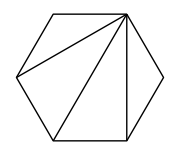
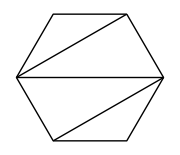
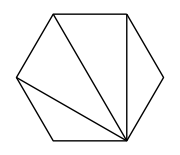
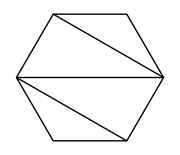
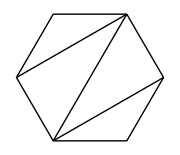
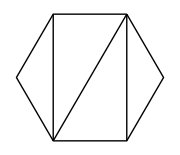
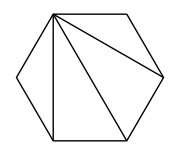
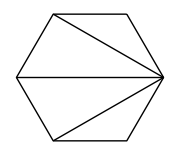
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[RegularPolygonTriangulations[6]]
```

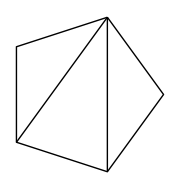
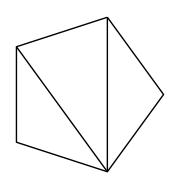
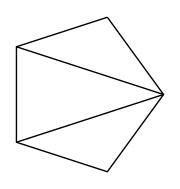
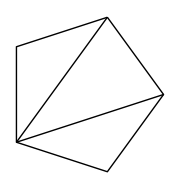
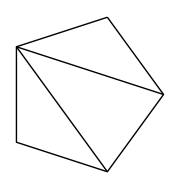
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Multicolumn[RegularPolygonTriangulations[5]]
```

```mathematica
Multicolumn[RegularPolygonTriangulations[6]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |

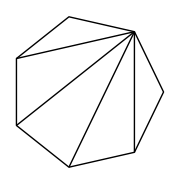
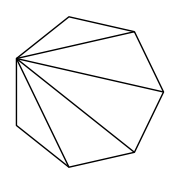
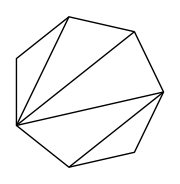
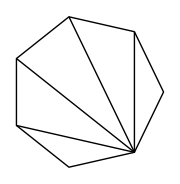
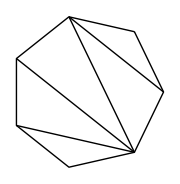
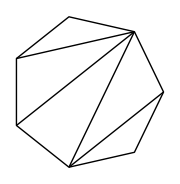
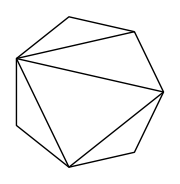
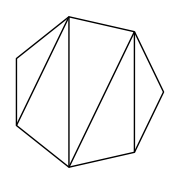
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[RegularPolygonTriangulations[7],{Automatic,5}]
```

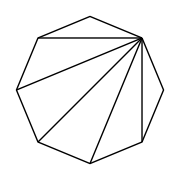
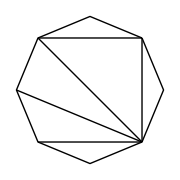
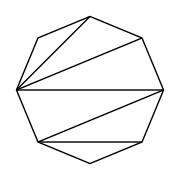
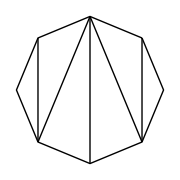
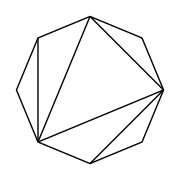
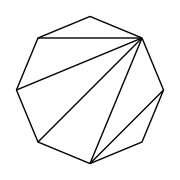
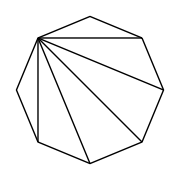
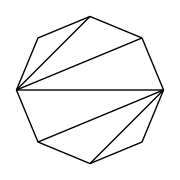
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[RegularPolygonTriangulations[8],{Automatic,5}]
```

```mathematica
Length[RegularPolygonTriangulations[8]]
```

132

```mathematica
Length[RegularPolygonTriangulations[9]]
```

2

```mathematica
RegularPolygonTriangulations[9]
```

{-Graphics-,-Graphics-}

```mathematica
?RegularPolygonTriangulations
```

```mathematica
?linechecker
```

```mathematica
?triangulations
```